```mathematica
(*PNJL Model*)
m0=5.5;          (*MeV*) 
T0=270;          (*MeV*) 
a0 = 6.75;
a1=-1.95;
a2 =2.625;
a3 =-7.44;
b3 =0.75;
b4=7.5;
=651 ;       (*MeV*)
G = 10.08*10^-6;       (*MeV^-2*)
Nf=2;
e[p_,z_] :=√(p^2+(m0-G*z)^2);
e1[p_,z_,mu_] :=√(p^2+(m0-G*z)^2)-mu;
e2[p_,z_,mu_] :=√(p^2+(m0-G*z)^2)+mu;
b2[T_]:=a0 + a1(T0/T)+a2(T0/T)^2+a3(T0/T)^3;
U[x_,T_] := ((-b2[T])/2*x^2-b3/3*(x^3)+b4/4*x^4)*T^4;
 [x_,z_,T_,mu_]:=U[x,T]+z^2/2*G-2*Nf*T*NIntegrate[p^2/(2*π^2)*(Log[1+3*x*ⅇ^(-e1[p,z,mu]/T)+3*x*ⅇ^(-2*e1[p,z,mu]/T)+ⅇ^(-3*e1[p,z,mu]/T)]+Log[1+3*x*ⅇ^(-e2[p,z,mu]/T)+3*x*ⅇ^(-2*e2[p,z,mu]/T)+ⅇ^(-3*e2[p,z,mu]/T)]),{p,0,∞}]-6* Nf*NIntegrate[p^2/(2*π^2)*e[p,z] ,{p,0,}];
```

```mathematica
(*data is of the form {{temperture(Mev),polyakovloop,sigma},...}*)
data ={{1,0.,1.},{2,0.,1.},{3,0.,1.},{4,0.,1.},{5,0.,1.},{6,0.,1.},{7,0.,1.},{8,0.,1.},{9,0.,1.},{10,0.,1.},{11,0.,1.},{12,0.,1.},{13,0.,1.},{14,0.,1.},{15,0.,1.},{16,0.,1.},{17,0.,1.},{18,0.,1.},{19,0.,1.},{20,0.,1.},{21,0.,1.},{22,0.,1.},{23,0.,1.},{24,0.,1.},{25,0.,1.},{26,-7.48261*10^-9,1.},{27,6.70004*10^-8,1.},{28,1.30072*10^-7,1.},{29,1.25104*10^-7,1.},{30,2.42226*10^-7,1.},{31,3.52169*10^-7,1.},{32,5.12603*10^-7,1.},{33,7.19285*10^-7,1.},{34,1.02234*10^-6,1.},{35,1.36194*10^-6,1.},{36,1.88875*10^-6,1.},{37,2.54491*10^-6,1.},{38,3.35527*10^-6,1.},{39,4.42056*10^-6,1.},{40,5.67583*10^-6,1.},{41,7.24414*10^-6,1.},{42,9.11537*10^-6,1.},{43,0.0000113641,1.},{44,0.0000141035,1.},{45,0.0000173185,1.},{46,0.0000210802,1.},{47,0.0000255175,1.},{48,0.00003062,1.},{49,0.0000365431,1.},{50,0.0000433582,1.},{51,0.0000510782,1.},{52,0.0000599078,1.},{53,0.0000698716,1.},{54,0.0000810875,1.},{55,0.0000936461,1.},{56,0.00010773,1.},{57,0.000123364,1.},{58,0.000140679,1.},{59,0.000159869,1.},{60,0.000180993,1.},{61,0.000204176,1.},{62,0.000229627,1.},{63,0.00025743,1.},{64,0.000287727,1.},{65,0.000320702,1.},{66,0.000356432,0.999999},{67,0.000395119,0.999999},{68,0.000436931,0.999999},{69,0.00048194,0.999998},{70,0.000530461,0.999998},{71,0.000582547,0.999997},{72,0.000638407,0.999997},{73,0.000698167,0.999996},{74,0.00076207,0.999995},{75,0.000830223,0.999994},{76,0.000902836,0.999993},{77,0.000980117,0.999992},{78,0.00106221,0.999991},{79,0.00114931,0.999989},{80,0.00124164,0.999987},{81,0.0013394,0.999985},{82,0.00144273,0.999983},{83,0.00155188,0.99998},{84,0.001667,0.999977},{85,0.00178837,0.999974},{86,0.00191614,0.99997},{87,0.00205052,0.999966},{88,0.00219179,0.999961},{89,0.0023401,0.999956},{90,0.00249568,0.99995},{91,0.00265876,0.999943},{92,0.00282956,0.999936},{93,0.00300836,0.999928},{94,0.00319532,0.999919},{95,0.00339072,0.999909},{96,0.00359478,0.999898},{97,0.00380779,0.999886},{98,0.00402995,0.999873},{99,0.00426148,0.999859},{100,0.00450269,0.999843},{101,0.00475383,0.999826},{102,0.00501515,0.999807},{103,0.00528693,0.999787},{104,0.00564602,0.999761},{105,0.00586291,0.99974},{106,0.00616763,0.999714},{107,0.0064839,0.999685},{108,0.00681208,0.999654},{109,0.00715235,0.999621},{110,0.00750509,0.999585},{111,0.00787042,0.999545},{112,0.00824901,0.999503},{113,0.00864087,0.999458},{114,0.00904636,0.999409},{115,0.00946593,0.999356},{116,0.00989974,0.999299},{117,0.0103483,0.999239},{118,0.0108119,0.999173},{119,0.0112908,0.999103},{120,0.0117855,0.999028},{121,0.012452,0.998936},{122,0.0128234,0.998862},{123,0.0133675,0.998771},{124,0.0139288,0.998673},{125,0.0146929,0.998551},{126,0.0151048,0.998457},{127,0.0157201,0.998338},{128,0.0163544,0.998212},{129,0.017008,0.998078},{130,0.0176813,0.997935},{131,0.0183749,0.997782},{132,0.0190891,0.997621},{133,0.0198245,0.99745},{134,0.0205816,0.997268},{135,0.0213608,0.997075},{136,0.0221626,0.99687},{137,0.0229875,0.996654},{138,0.0238361,0.996424},{139,0.0247091,0.996182},{140,0.0256069,0.995925},{141,0.0265301,0.995653},{142,0.0274793,0.995366},{143,0.0284551,0.995063},{144,0.0294581,0.994743},{145,0.0304891,0.994404},{146,0.0315486,0.994048},{147,0.0326372,0.993672},{148,0.0337561,0.993275},{149,0.0349052,0.992856},{150,0.0360859,0.992416},{151,0.0372989,0.991951},{152,0.0385446,0.991463},{153,0.0398242,0.990948},{154,0.0411384,0.990406},{155,0.042488,0.989837},{156,0.0438739,0.989237},{157,0.0452971,0.988607},{158,0.0467584,0.987944},{159,0.0482591,0.987247},{160,0.0497996,0.986516},{161,0.0513816,0.985747},{162,0.0530057,0.984939},{163,0.0546731,0.984091},{164,0.0563851,0.9832},{165,0.0581425,0.982265},{166,0.0599468,0.981284},{167,0.0617993,0.980254},{168,0.0637011,0.979173},{169,0.0656535,0.978039},{170,0.0676581,0.976849},{171,0.0697166,0.9756},{172,0.0718289,0.974292},{173,0.0739982,0.972919},{174,0.0762254,0.971479},{175,0.0785121,0.969969},{176,0.0808601,0.968386},{177,0.083271,0.966726},{178,0.0857463,0.964986},{179,0.0882885,0.963161},{180,0.0908988,0.961248},{181,0.0935794,0.959242},{182,0.0963322,0.957139},{183,0.099159,0.954935},{184,0.102063,0.952622},{185,0.105044,0.950199},{186,0.108107,0.947658},{187,0.111252,0.944992},{188,0.114483,0.942197},{189,0.117802,0.939266},{190,0.12121,0.936192},{191,0.124712,0.932967},{192,0.128308,0.929585},{193,0.132002,0.926036},{194,0.135796,0.922312},{195,0.139693,0.918404},{196,0.143695,0.914303},{197,0.147806,0.909998},{198,0.152028,0.905478},{199,0.156362,0.900733},{200,0.160814,0.895748},{201,0.165384,0.890516},{202,0.170075,0.885016},{203,0.17489,0.879238},{204,0.179832,0.873167},{205,0.184901,0.866786},{206,0.190102,0.860077},{207,0.195435,0.853024},{208,0.200902,0.845606},{209,0.206504,0.837804},{210,0.212244,0.829597},{211,0.218122,0.820961},{212,0.224139,0.811874},{213,0.230293,0.802308},{214,0.236587,0.792241},{215,0.243018,0.781637},{216,0.249586,0.770474},{217,0.256289,0.758717},{218,0.263124,0.746336},{219,0.270089,0.733292},{220,0.277181,0.719553},{221,0.284395,0.705079},{222,0.291726,0.689832},{223,0.299171,0.673772},{224,0.306721,0.656858},{225,0.314372,0.639049},{226,0.322115,0.620305},{227,0.329944,0.600588},{228,0.337851,0.579869},{229,0.345826,0.558123},{230,0.353862,0.535341},{231,0.361949,0.511533},{232,0.370079,0.48674},{233,0.378242,0.461044},{234,0.386427,0.43459},{235,0.394628,0.407587},{236,0.402833,0.380307},{237,0.411037,0.353136},{238,0.419225,0.326481},{239,0.427394,0.300784},{240,0.435534,0.276445},{241,0.443638,0.253784},{242,0.451698,0.232952},{243,0.459708,0.214067},{244,0.467661,0.197068},{245,0.475552,0.181859},{246,0.483374,0.168268},{247,0.491125,0.156145},{248,0.498799,0.145306},{249,0.506392,0.135605},{250,0.513902,0.126893},{251,0.521324,0.11906},{252,0.528657,0.111961},{253,0.535897,0.105545},{254,0.543045,0.0996939},{255,0.550097,0.0943605},{256,0.557052,0.0894633},{257,0.563911,0.0849668},{258,0.570672,0.0808284},{259,0.577335,0.077027},{260,0.583899,0.073484},{261,0.589712,0.0703506},{262,0.596734,0.067142},{263,0.603004,0.0642608},{264,0.661935,0.0527476},{265,0.615255,0.0590983},{266,0.621236,0.0567609},{267,0.627123,0.0545476},{268,0.632915,0.0524777},{269,0.638616,0.0505189},{270,0.644224,0.0486472},{271,0.649742,0.0469023},{272,0.655171,0.0452171},{273,0.660512,0.0436368},{274,0.665766,0.0421241},{275,0.670935,0.0406925},{276,0.67602,0.0393445},{277,0.681022,0.0380379},{278,0.685942,0.0367647},{279,0.690784,0.0355861},{280,0.695546,0.0344409},{281,0.700231,0.0333594},{282,0.70484,0.0323017},{283,0.709374,0.031299},{284,0.713836,0.0303494},{285,0.718225,0.0294149},{286,0.722544,0.0285136},{287,0.726794,0.0276515},{288,0.730976,0.0268378},{289,0.735091,0.0260214},{290,0.73914,0.0252487},{291,0.743125,0.0244957},{292,0.747048,0.0237988},{293,0.750909,0.0230874},{294,0.754709,0.0224077},{295,0.75845,0.0217612},{296,0.762132,0.0211091},{297,0.765757,0.0205267},{298,0.769326,0.0199206},{299,0.77284,0.0193522},{300,0.7763,0.0188129},{301,0.779707,0.0182265},{302,0.783062,0.0177485},{303,0.786367,0.0172071},{304,0.789621,0.0167721},{305,0.792826,0.0162773},{306,0.795983,0.0157518},{307,0.799093,0.0152838},{308,0.802157,0.0148767},{309,0.805175,0.0144433},{310,0.808148,0.0139806},{311,0.811078,0.0135795},{312,0.813965,0.013209},{313,0.81681,0.0127487},{314,0.819614,0.012355},{315,0.822377,0.0120194},{316,0.8251,0.0116651},{317,0.827785,0.0113434},{318,0.830431,0.0109579},{319,0.833039,0.010612},{320,0.83561,0.0102678},{321,0.838146,0.0099438},{322,0.840645,0.00960738},{323,0.84311,0.00931563},{324,0.84554,0.00902539},{325,0.847936,0.00871604},{326,0.8503,0.00841396},{327,0.852631,0.00810091},{328,0.85493,0.00784453},{329,0.857197,0.00756038},{330,0.859434,0.0073933},{331,0.861641,0.0070549},{332,0.863818,0.00677517},{333,0.865965,0.00649675},{334,0.868084,0.00629859},{335,0.870175,0.00603031},{336,0.872238,0.00564216},{337,0.874274,0.00555134},{338,0.876283,0.00534338},{339,0.878266,0.00518817},{340,0.880222,0.00488306},{341,0.882154,0.00469278},{342,0.88406,0.00449174},{343,0.885942,0.00434208},{344,0.8878,0.00403942},{345,0.889634,0.00395321},{346,0.891445,0.0034594},{347,0.893233,0.00339225},{348,0.894997,0.00322151},{349,0.89674,0.00307455},{350,0.898461,0.00286823},{351,0.900161,0.00265857},{352,0.901839,0.0024785},{353,0.903497,0.00229947},{354,0.905134,0.00219601},{355,0.906751,0.00195179},{356,0.908349,0.00179115},{357,0.909926,0.0016046},{358,0.911485,0.00142427},{359,0.913024,0.00129945},{360,0.914546,0.00106967},{361,0.916049,0.000765237},{362,0.917533,0.000839047},{363,0.919001,0.000622597},{364,0.92045,0.000635919},{365,0.921883,0.000443539},{366,0.923298,0.000151297},{367,0.924697,0.000312161},{368,0.92608,-0.000261169},{369,0.927592,-0.000189167},{370,0.928798,-0.000330912},{371,0.930133,-0.000363926},{372,0.931452,-0.0000622853},{373,0.932757,-0.000751527},{374,0.934046,-0.000826804},{375,0.935321,-0.000936787},{376,0.936581,-0.00164614},{377,0.937827,-0.00128644},{378,0.939059,-0.0000196817},{379,0.940278,-0.00152657},{380,0.941482,-0.00183896},{381,0.942673,-0.00183041},{382,0.943851,-0.00184613},{383,0.945015,-0.00197577},{384,0.946167,-0.00206506},{385,0.947306,-0.00250599},{386,0.948433,-0.00228323},{387,0.949547,-0.0024242},{388,0.950649,-0.0026864},{389,0.95174,-0.00263583},{390,0.952818,-0.0026575},{391,0.953885,-0.00284714},{392,0.95494,-0.00295021},{393,0.955984,-0.00310057},{394,0.957017,-0.00318029},{395,0.958038,-0.00329508},{396,0.959049,-0.00316465},{397,0.96005,-0.00353458},{398,0.961039,-0.00354615},{399,0.962019,-0.00373311},{400,0.962988,-0.0037795},{401,0.963947,-0.00385002},{402,0.964896,-0.00391324},{403,0.977885,-0.00413366},{404,0.966765,-0.00408318},{405,0.967684,-0.00421941},{406,0.968595,-0.00428118},{407,0.969496,-0.00434349},{408,0.970388,-0.00454091},{409,0.971271,-0.00450466},{410,0.972145,-0.0046165},{411,0.97301,-0.00462847},{412,0.973866,-0.00490511},{413,0.974714,-0.00485049},{414,0.975554,-0.00494311},{415,0.976385,-0.00503637},{416,0.977207,-0.0050962},{417,0.978022,-0.00517025},{418,0.978829,-0.00524823},{419,0.979627,-0.00533661},{420,0.980418,-0.00540022},{421,0.981201,-0.00547669},{422,0.981976,-0.00554544},{423,0.982744,-0.00564562},{424,0.983505,-0.0056798},{425,0.984258,-0.00572908},{426,0.985004,-0.00583915},{427,0.985742,-0.00590364},{428,0.986474,-0.00592768},{429,0.987199,-0.00606082},{430,0.987916,-0.0061097},{431,0.988627,-0.00616109},{432,0.989331,-0.00625238},{433,0.990029,-0.00631879},{434,0.99072,-0.00636036},{435,0.991404,-0.00647932},{436,0.992083,-0.00651161},{437,0.992754,-0.00655324},{438,0.99342,-0.006581},{439,0.994079,-0.0067349},{440,0.994733,-0.00674558},{441,0.99538,-0.00666034},{442,0.996022,-0.00686417},{443,0.996657,-0.00693327},{444,0.997287,-0.00694797},{445,0.997911,-0.00704703},{446,0.998529,-0.00711121},{447,0.999142,-0.00715773},{448,0.999749,-0.0072197},{449,1.00035,-0.00726172},{450,1.00095,-0.00731909},{451,1.00154,-0.00738649},{452,1.00212,-0.00743504},{453,1.0027,-0.0074886},{454,1.00328,-0.00753382},{455,1.00008,-0.00754158},{456,1.00442,-0.00762277},{457,1.00498,-0.00772113},{458,1.00553,-0.00772629},{459,1.00608,-0.00781285},{460,1.00663,-0.00787983},{461,1.00717,-0.00787417},{462,1.00771,-0.00796495},{463,1.00824,-0.00801206},{464,1.00876,-0.00805836},{465,1.00929,-0.00807439},{466,1.00981,-0.00819459},{467,1.01032,-0.00817638},{468,1.01083,-0.00819664},{469,1.01133,-0.00830124},{470,1.01183,-0.00838949},{471,1.01233,-0.00839732},{472,1.01282,-0.00843401},{473,1.01331,-0.00848323},{474,1.0138,-0.00854061},{475,1.01428,-0.00857317},{476,1.01475,-0.00861875},{477,1.01522,-0.00866166},{478,1.01569,-0.00867989},{479,1.01616,-0.00876267},{480,1.01662,-0.00876404},{481,1.01707,-0.00880443},{482,1.01753,-0.00887567},{483,1.01798,-0.00891764},{484,1.01842,-0.00895625},{485,1.01886,-0.00900385},{486,1.0193,-0.00905037},{487,1.01974,-0.00908462},{488,1.02017,-0.00912405},{489,1.0206,-0.00918648},{490,1.02102,-0.00919921},{491,1.02144,-0.00917964},{492,1.02186,-0.00919496},{493,1.02228,-0.00930539},{494,1.02269,-0.00935252},{495,1.0231,-0.00940726},{496,1.0235,-0.00941617},{497,1.0239,-0.00943773},{498,1.0243,-0.00944083},{499,1.03183,-0.00957939},{500,1.02509,-0.00958951},{501,1.02548,-0.00966332},{502,1.02586,-0.00965294},{503,1.02625,-0.00969526},{504,1.02663,-0.00972178},{505,1.027,-0.00975081},{506,1.02738,-0.00979821},{507,1.02775,-0.00983568},{508,1.02812,-0.00985551},{509,1.02848,-0.00993327},{510,1.02885,-0.00992892},{511,1.02921,-0.00991467},{512,1.02957,-0.0099981},{513,1.02992,-0.0100259},{514,1.03027,-0.0100638},{515,1.03726,-0.0101276},{516,1.03097,-0.010127},{517,1.03131,-0.0101549},{518,1.03166,-0.010192},{519,1.03199,-0.0102367},{520,1.03233,-0.010257},{521,1.03267,-0.0102884},{522,1.033,-0.0103759},{523,1.03333,-0.0103344},{524,1.03365,-0.0103788},{525,1.03398,-0.0104143},{526,1.0343,-0.0104333},{527,1.03462,-0.0105716},{528,1.03494,-0.0104945},{529,1.03525,-0.0104884},{530,1.03557,-0.0105598},{531,1.03588,-0.010588},{532,1.03619,-0.010544},{533,1.03649,-0.0106521},{534,1.0368,-0.0106781},{535,1.0371,-0.0106563},{536,1.0374,-0.0107314},{537,1.0377,-0.0107628},{538,1.03799,-0.0108417},{539,1.03828,-0.0108065},{540,1.03858,-0.0108332},{541,1.03887,-0.0109112},{542,1.03915,-0.0108965},{543,1.03944,-0.0109324},{544,1.03972,-0.0109794},{545,1.04,-0.0109719},{546,1.04028,-0.010957},{547,1.04056,-0.0110279},{548,1.04083,-0.0110545},{549,1.04111,-0.0110651},{550,1.04138,-0.0110327},{551,1.04165,-0.0111307},{552,1.04192,-0.0111495},{553,1.04218,-0.0111816},{554,1.04245,-0.0112255},{555,1.04271,-0.0111981},{556,1.04297,-0.0112515},{557,1.04323,-0.0112772},{558,1.04349,-0.0113307},{559,1.04374,-0.0113249},{560,1.044,-0.0113485},{561,1.04425,-0.0114073},{562,1.0445,-0.0114005},{563,1.04475,-0.0114195},{564,1.045,-0.0114466},{565,1.04524,-0.0114684},{566,1.04549,-0.0115027},{567,1.04573,-0.0115029},{568,1.04597,-0.0115604},{569,1.04623,-0.0115979},{570,1.04645,-0.0115823},{571,1.04668,-0.0115711},{572,1.04692,-0.0115979},{573,1.04715,-0.0116594},{574,1.04738,-0.0116727},{575,1.04761,-0.0116945},{576,1.04784,-0.011711},{577,1.04807,-0.0117304},{578,1.04829,-0.0117263},{579,1.04852,-0.0117722},{580,1.04874,-0.0118417},{581,1.04896,-0.0118041},{582,1.04918,-0.0118439},{583,1.0494,-0.0118585},{584,1.04962,-0.0118646},{585,1.04983,-0.0119004},{586,1.05005,-0.0119148},{587,1.05026,-0.0119542},{588,1.05047,-0.0119249},{589,1.05068,-0.0119838},{590,1.05089,-0.0119268},{591,1.0511,-0.0120302},{592,1.0513,-0.0120262},{593,1.05151,-0.0120965},{594,1.05171,-0.0120886},{595,1.05191,-0.0121176},{596,1.05212,-0.0122158},{597,1.05232,-0.012144},{598,1.05251,-0.0121668},{599,1.05271,-0.0121967},{600,1.05291,-0.0121944}};
```

```mathematica
Tmp = data[[All,1]];
polyakovdata = data[[All,2]];
sigmadata = data[[All,3]]*-3.195*10^7;
```

```mathematica
Series[Log[1+3*x*ⅇ^(-(b[p]-a))+3*x*ⅇ^(-2*(b[p]-a))+ⅇ^(-3*(b[p]-a))]+Log[1+3*x*ⅇ^(-(b[p]+a))+3*x*ⅇ^(-2*(b[p]+a))+ⅇ^(-3*(b[p]+a))],{a,0,8}]//ExpandAll
```

2 Log[1+ⅇ^(-3 b[p])+3 ⅇ^(-2 b[p]) x+3 ⅇ^(-b[p]) x]+((9 ⅇ^(3 b[p]))/(1+2 ⅇ^(3 b[p])+ⅇ^(6 b[p])+6 ⅇ^b[p] x+6 ⅇ^(2 b[p]) x+6 ⅇ^(4 b[p]) x+6 ⅇ^(5 b[p]) x+9 ⅇ^(2 b[p]) x^2+18 ⅇ^(3 b[p]) x^2+9 ⅇ^(4 b[p]) x^2)+(3 ⅇ^b[p] x)/(1+2 ⅇ^(3 b[p])+ⅇ^(6 b[p])+6 ⅇ^b[p] x+6 ⅇ^(2 b[p]) x+6 ⅇ^(4 b[p]) x+6 ⅇ^(5 b[p]) x+9 ⅇ^(2 b[p]) x^2+18 ⅇ^(3 b[p]) x^2+9 ⅇ^(4 b[p]) x^2)+(12 ⅇ^(2 b[p]) x)/(1+2 ⅇ^(3 b[p])+ⅇ^(6 b[p])+6 ⅇ^b[p] x+6 ⅇ^(2 b[p]) x+6 ⅇ^(4 b[p]) x+6 ⅇ^(5 b[p]) x+9 ⅇ^(2 b[p]) x^2+18 ⅇ^(3 b[p]) x^2+9 ⅇ^(4 b[p]) x^2)+(12 ⅇ^(4 b[p]) x)/(1+2 ⅇ^(3 b[p])+ⅇ^(6 b[p])+6 ⅇ^b[p] x+6 ⅇ^(2 b[p]) x+6 ⅇ^(4 b[p]) x+6 ⅇ^(5 b[p]) x+9 ⅇ^(2 b[p]) x^2+18 ⅇ^(3 b[p]) x^2+9 ⅇ^(4 b[p]) x^2)+(3 ⅇ^(5 b[p]) x)/(1+2 ⅇ^(3 b[p])+ⅇ^(6 b[p])+6 ⅇ^b[p] x+6 ⅇ^(2 b[p]) x+6 ⅇ^(4 b[p]) x+6 ⅇ^(5 b[p]) x+9 ⅇ^(2 b[p]) x^2+18 ⅇ^(3 b[p]) x^2+9 ⅇ^(4 b[p]) x^2)+(9 ⅇ^(3 b[p]) x^2)/(1+2 ⅇ^(3 b[p])+ⅇ^(6 b[p])+6 ⅇ^b[p] x+6 ⅇ^(2 b[p]) x+6 ⅇ^(4 b[p]) x+6 ⅇ^(5 b[p]) x+9 ⅇ^(2 b[p]) x^2+18 ⅇ^(3 b[p]) x^2+9 ⅇ^(4 b[p]) x^2)) a^2+((27 ⅇ^(-3 1))/(4 (1+ⅇ^1+3 ⅇ^1 x+3 ⅇ^(-b[p]) x))+97+(27 ⅇ^611 x^3)/(2 (1) (1))) a^4+1+(4028+1/1+2187/(4 (1) (8+32+648 ⅇ^1 x^4))+(2187 ⅇ^b[p] x)/1+(2187 ⅇ^(2 b[p]) x)/(4 (1+ⅇ^1+1+3 ⅇ^(2 1) x) (8+32 ⅇ^(3 b[p])+48 ⅇ^(6 b[p])+32 ⅇ^(9 b[p])+8 ⅇ^(12 b[p])+96 ⅇ^b[p] x+23+648 ⅇ^(4 b[p]) x^4+2592 ⅇ^(5 b[p]) x^4+3888 ⅇ^(6 b[p]) x^4+2592 ⅇ^(7 b[p]) x^4+648 ⅇ^(8 b[p]) x^4))) a^8+O[a]^9
 |  |  |  |

```mathematica
clist =CoefficientList[%50,a];
clist
```

{2 Log[1+ⅇ^(-1/200 √(2.47345+p^2))+3.15873 ⅇ^(-1/300 √(2.47345+p^2))+3.15873 ⅇ^(-1/600 √(2.47345+p^2))],0,5,0,2598+1/1+2187/(4 (1+2+ⅇ^1) (8+11+8 ⅇ^1))+(1151.36 ⅇ^(1/600 √(2.47345+p^2)))/((1+3.15873 ⅇ^(1/600 √(2.47345+p^2))+3.15873 ⅇ^(1/300 √1)+ⅇ^(1/200 √(2.47345+p^2))) (8+11+8 ⅇ^(1/50 1)))+(575.679 ⅇ^(1/300 √(2.47345+p^2)))/((1+3.15873 ⅇ^(1/600 √(2.47345+p^2))+3.15873 ⅇ^(1/300 √(2.47345+p^2))+ⅇ^(1/200 √(2.47345+p^2))) (8+101.079 ⅇ^(1/600 √(2.47345+p^2))+580.003 ⅇ^(1/300 √(2.47345+p^2))+8+101.079 ⅇ^(11/600 √(2.47345+p^2))+8 ⅇ^(1/50 √(2.47345+p^2))))}
 |  |  |  |

```mathematica
c[t_,j_]:=Module[{list}, x =polyakovdata[[t]];
b[p_]:= e[p,sigmadata[[t]]]/Tmp[[t]];
2*Nf/((Tmp^3)[[t]])*NIntegrate[p^2/(2*π^2)*(clist[[j]]),{p,0,∞}]
];
```

```mathematica
n=Length[Tmp];
progress=0;
start=AbsoluteTime[];
PrintTemporary@Dynamic@Row[{ProgressIndicator[progress,{0,n}],"  Running time: ",Round[AbsoluteTime[]-start]," seconds"}];

coef=Table[progress=i;
{Tmp[[i]]/Tc,c[i,3],c[i,5],c[i,7],c[i,9]},{i,n}];
```

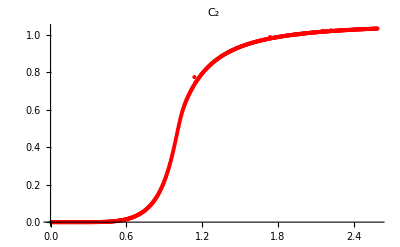

```mathematica
ListPlot[Transpose[{coef[[All,1]],coef[[All,2]]}],PlotRange->All,PlotStyle->Red,PlotLabel->]
```

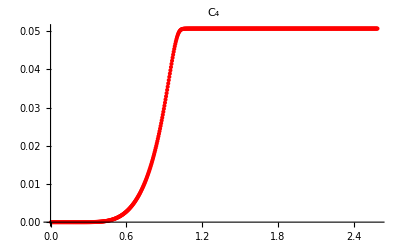

```mathematica
ListPlot[Transpose[{coef[[All,1]],coef[[All,3]]}],PlotRange->All,PlotStyle->Red,PlotLabel->]
```

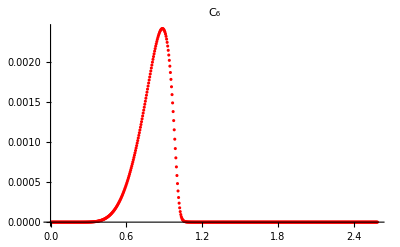

```mathematica
ListPlot[Transpose[{coef[[All,1]],coef[[All,4]]}],PlotRange->All,PlotStyle->Red,PlotLabel->]
```

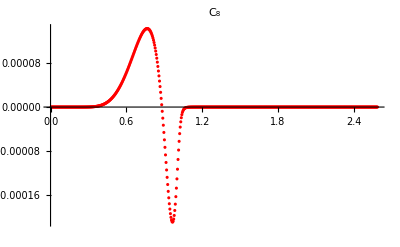

```mathematica
ListPlot[Transpose[{coef[[All,1]],coef[[All,5]]}],PlotRange->All,PlotStyle->Red,PlotLabel->]
```